```mathematica
$Assumptions={}
FullSimplify[Integrate[x^n Exp[-a x],{x,0,Infinity}]]
```

{}

ConditionalExpression[a^(-1-n) Gamma[1+n],Re[n]>-1&&Re[a]>0]

```mathematica
Legended[Plot[x^2,{x,0,2},PlotStyle->Thickness[.02]],SwatchLegend[{Blue},{"Name"}]]
```

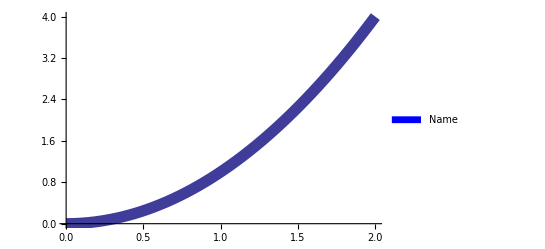

-Graphics-

```mathematica
Export["plot.png",%12,ImageResolution->450]
```

plot.png

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["plot.png"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["plot.png"]]]
```

```mathematica
BarChart[{1,2,3,2,Legended[Style[3,Orange],"important"],5,2,6}]
```

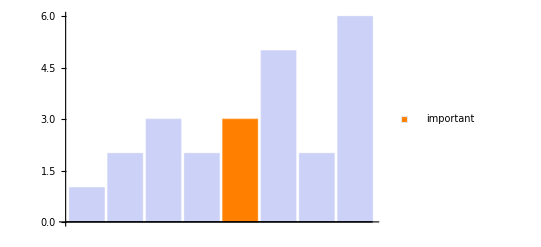

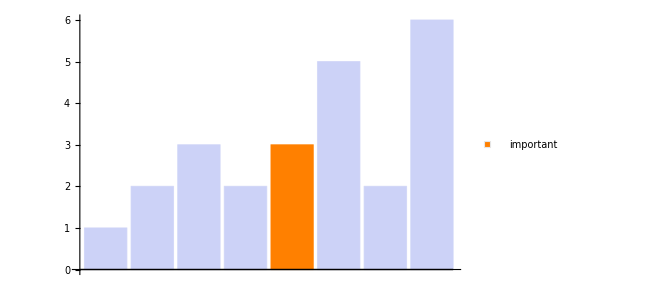

-Graphics-

```mathematica
Export["plot.png",%20,ImageResolution->450]
```

plot.png

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["plot.png"]]]
```

```mathematica
v=Quantity[0.75,"speed of light"]
UnitConvert[v,"meters/second"]
```

0.75

2.24844×10^8

```mathematica
Integrate[2Pi r,{r,Quantity[0,"m"],Quantity[10,"m"]}]
```

100 π

```mathematica
Grad[r Sin[t]Sin[p],{r,t,p},"Spherical"]
```

{Sin[p] Sin[t],Cos[t] Sin[p],Cos[p]}

```mathematica
WolframAlpha["ISS","PodIDs"]
```

{Input,Position:SatelliteData,OrbitalInformation:SatelliteData,OtherInformation:SatelliteData,Image:SatelliteData,SkyMap:SatelliteData}

```mathematica
WolframAlpha["ISS",{{"SkyMap:SatelliteData",1},"ComputableData"}]
```

{{not currently visible},{{{altitude,-30.36},{azimuth,312.1},{next rise,1:49 pm CDT  |  Thursday, April 24, 2014},{next set,2:00 pm CDT  |  Thursday, April 24, 2014},{constellation,Orion}}}}

```mathematica
WolframAlpha["GOOG closing price","PodIDs"]
```

{Input,Result,HistoryDaily:Close:FinancialData}

```mathematica
DateListPlot[WolframAlpha[#<>" closing price",{{"HistoryDaily:Close:FinancialData",1},"TimeSeriesData"}]&/@{"DIS","LUV","MSFT"},PlotLegends->{"DIS","LUV","MSFT"}]
```

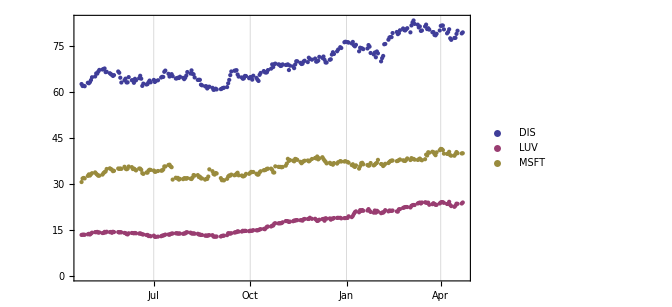

-Graphics-

```mathematica
Export["stocks.png",%56,ImageResolution->450]
```

stocks.png

```mathematica
StringTake[ExampleData[{"Text","ShakespearesSonnets"}],611]
```

I From fairest creatures we desire increase, That thereby beauty's rose might never die, But as the riper should by time decease, His tender heir might bear his memory: But thou contracted to thine own bright eyes, Feed'st thy light's flame with self-substantial fuel, Making a famine where abundance lies, Thy self thy foe, to thy sweet self too cruel: Thou that art now the world's fresh ornament, And only herald to the gaudy spring, Within thine own bud buriest thy content, And tender churl mak'st waste in niggarding: Pity the world, or else this glutton be, To eat the world's due, by the grave and thee.

```mathematica
ElementData["Nitrogen","ElectronConfigurationString"]
```

[He]2s^22p^3

```mathematica
UnitConvert[Quantity[IsotopeData[#1,#2],IsotopeData[#1,#2,"Units"]],"years"]&["C14","HalfLife"]
```

5700.

```mathematica
MatrixForm[{Row[ParticleData[#,"FullSymbol"]&/@#[[1]]],#[[2]]}&/@ParticleData[#,"DecayModes"]&["KLong"]]
```

(π^0π^0π^0 | 0.1952
π^+π^-π^0 | 0.1254
π^0π^0γ | 0.
π^+π^-γ | 0.0000415
π^0γγ | 1.32×10^-6
π^0γe^+e^- | 1.62×10^-8
γγ | 0.000547
γγγ | 0.
e^+e^-γ | 9.5×10^-6
μ^+μ^-γ | 3.59×10^-7
e^+e^-γγ | 5.95×10^-7
μ^+μ^-γγ | 1.×10^-8)

```mathematica
Export["matrix.png",%98,ImageResolution->450]
```

matrix.png